```mathematica
Integrate[Exp[-s]Sin[v1 s](1+b Cos[v2 s]),{s,0,Infinity}]
```

ConditionalExpression[v1/(1+v1^2)+1/2 b ((v1-v2)/(1+(v1-v2)^2)+(v1+v2)/(1+(v1+v2)^2)),Abs[Im[v1]]+Abs[Im[v2]]<1]

```mathematica
Solve[√(-1+1.8 g)==0,g]
```

{{g→0.555556}}

```mathematica
Solve[{-v1+g(v1/(1+v1^2)+1/2 b ((v1-v2)/(1+(v1-v2)^2)+(v1+v2)/(1+(v1+v2)^2)))==0,-v2+g(v2/(1+v2^2)+1/2 b ((v2-v1)/(1+(v2-v1)^2)+(v2+v1)/(1+(v2+v1)^2)))==0},{v1,v2}]/.b->.8
```

{{v1→-√(-1+1.8 g),v2→0},{v1→√(-1+1.8 g),v2→0},{v1→-(√(-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2)))/(2 √2),v2→-1/(√(-68. g^3-71.44 g^4-18.72 g^5))(√(32. g-107.04 g^2+189.392 g^3-112.08 g^4-123.552 g^5-10 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))+63.2 g (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))-119.68 g^2 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))+113.35 g^3 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))+2.858 g^4 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))-50.076 g^5 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))-125/16 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^2+29.3438 g (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^2-38.1525 g^2 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^2+10.6848 g^3 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^2+16.699 g^4 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^2-2.184 g^5 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^2-105/64 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^3+4.37656 g (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^3-3.11594 g^2 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^3-1.64763 g^3 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^3+0.7735 g^4 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^3-(125 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^4)/1024+0.231934 g (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^4+0.0046875 g^2 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^4-0.08125 g^3 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^4-(5 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^5)/2048+0.0034668 g (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^5+0.00253906 g^2 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^5))},{v1→-(√(-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2)))/(2 √2),v2→1/(√(-68. g^3-71.44 g^4-18.72 g^5))(√(32. g-107.04 g^2+189.392 g^3-112.08 g^4-123.552 g^5-10 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))+63.2 g (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))-119.68 g^2 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))+113.35 g^3 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))+2.858 g^4 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))-50.076 g^5 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))-125/16 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^2+29.3438 g (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^2-38.1525 g^2 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^2+10.6848 g^3 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^2+16.699 g^4 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^2-2.184 g^5 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^2-105/64 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^3+4.37656 g (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^3-3.11594 g^2 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^3-1.64763 g^3 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^3+0.7735 g^4 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^3-(125 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^4)/1024+0.231934 g (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^4+0.0046875 g^2 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^4-0.08125 g^3 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^4-(5 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^5)/2048+0.0034668 g (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^5+0.00253906 g^2 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^5))},{v1→(√(-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2)))/(2 √2),v2→-1/(√(-68. g^3-71.44 g^4-18.72 g^5))(√(32. g-107.04 g^2+189.392 g^3-112.08 g^4-123.552 g^5-10 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))+63.2 g (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))-119.68 g^2 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))+113.35 g^3 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))+2.858 g^4 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))-50.076 g^5 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))-125/16 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^2+29.3438 g (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^2-38.1525 g^2 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^2+10.6848 g^3 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^2+16.699 g^4 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^2-2.184 g^5 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^2-105/64 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^3+4.37656 g (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^3-3.11594 g^2 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^3-1.64763 g^3 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^3+0.7735 g^4 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^3-(125 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^4)/1024+0.231934 g (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^4+0.0046875 g^2 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^4-0.08125 g^3 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^4-(5 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^5)/2048+0.0034668 g (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^5+0.00253906 g^2 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^5))},{v1→(√(-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2)))/(2 √2),v2→1/(√(-68. g^3-71.44 g^4-18.72 g^5))(√(32. g-107.04 g^2+189.392 g^3-112.08 g^4-123.552 g^5-10 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))+63.2 g (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))-119.68 g^2 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))+113.35 g^3 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))+2.858 g^4 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))-50.076 g^5 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))-125/16 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^2+29.3438 g (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^2-38.1525 g^2 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^2+10.6848 g^3 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^2+16.699 g^4 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^2-2.184 g^5 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^2-105/64 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^3+4.37656 g (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^3-3.11594 g^2 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^3-1.64763 g^3 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^3+0.7735 g^4 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^3-(125 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^4)/1024+0.231934 g (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^4+0.0046875 g^2 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^4-0.08125 g^3 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^4-(5 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^5)/2048+0.0034668 g (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^5+0.00253906 g^2 (-5+4.8 g-√(16 (-1+1.8 g)+(-5+4.8 g)^2))^5))},{v1→-(√(-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2)))/(2 √2),v2→-1/(√(-68. g^3-71.44 g^4-18.72 g^5))(√(32. g-107.04 g^2+189.392 g^3-112.08 g^4-123.552 g^5-10 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))+63.2 g (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))-119.68 g^2 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))+113.35 g^3 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))+2.858 g^4 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))-50.076 g^5 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))-125/16 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^2+29.3438 g (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^2-38.1525 g^2 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^2+10.6848 g^3 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^2+16.699 g^4 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^2-2.184 g^5 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^2-105/64 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^3+4.37656 g (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^3-3.11594 g^2 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^3-1.64763 g^3 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^3+0.7735 g^4 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^3-(125 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^4)/1024+0.231934 g (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^4+0.0046875 g^2 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^4-0.08125 g^3 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^4-(5 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^5)/2048+0.0034668 g (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^5+0.00253906 g^2 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^5))},{v1→-(√(-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2)))/(2 √2),v2→1/(√(-68. g^3-71.44 g^4-18.72 g^5))(√(32. g-107.04 g^2+189.392 g^3-112.08 g^4-123.552 g^5-10 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))+63.2 g (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))-119.68 g^2 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))+113.35 g^3 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))+2.858 g^4 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))-50.076 g^5 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))-125/16 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^2+29.3438 g (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^2-38.1525 g^2 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^2+10.6848 g^3 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^2+16.699 g^4 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^2-2.184 g^5 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^2-105/64 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^3+4.37656 g (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^3-3.11594 g^2 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^3-1.64763 g^3 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^3+0.7735 g^4 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^3-(125 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^4)/1024+0.231934 g (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^4+0.0046875 g^2 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^4-0.08125 g^3 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^4-(5 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^5)/2048+0.0034668 g (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^5+0.00253906 g^2 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^5))},{v1→(√(-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2)))/(2 √2),v2→-1/(√(-68. g^3-71.44 g^4-18.72 g^5))(√(32. g-107.04 g^2+189.392 g^3-112.08 g^4-123.552 g^5-10 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))+63.2 g (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))-119.68 g^2 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))+113.35 g^3 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))+2.858 g^4 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))-50.076 g^5 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))-125/16 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^2+29.3438 g (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^2-38.1525 g^2 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^2+10.6848 g^3 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^2+16.699 g^4 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^2-2.184 g^5 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^2-105/64 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^3+4.37656 g (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^3-3.11594 g^2 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^3-1.64763 g^3 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^3+0.7735 g^4 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^3-(125 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^4)/1024+0.231934 g (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^4+0.0046875 g^2 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^4-0.08125 g^3 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^4-(5 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^5)/2048+0.0034668 g (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^5+0.00253906 g^2 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^5))},{v1→(√(-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2)))/(2 √2),v2→1/(√(-68. g^3-71.44 g^4-18.72 g^5))(√(32. g-107.04 g^2+189.392 g^3-112.08 g^4-123.552 g^5-10 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))+63.2 g (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))-119.68 g^2 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))+113.35 g^3 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))+2.858 g^4 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))-50.076 g^5 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))-125/16 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^2+29.3438 g (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^2-38.1525 g^2 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^2+10.6848 g^3 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^2+16.699 g^4 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^2-2.184 g^5 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^2-105/64 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^3+4.37656 g (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^3-3.11594 g^2 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^3-1.64763 g^3 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^3+0.7735 g^4 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^3-(125 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^4)/1024+0.231934 g (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^4+0.0046875 g^2 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^4-0.08125 g^3 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^4-(5 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^5)/2048+0.0034668 g (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^5+0.00253906 g^2 (-5+4.8 g+√(16 (-1+1.8 g)+(-5+4.8 g)^2))^5))},{v1→-√(-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2)))),v2→-1/(√(-68. g^3-71.44 g^4-18.72 g^5))(√(32. g-107.04 g^2+189.392 g^3-112.08 g^4-123.552 g^5-80 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))+505.6 g (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))-957.44 g^2 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))+906.8 g^3 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))+22.864 g^4 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))-400.608 g^5 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))-500 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2+1878. g (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2-2441.76 g^2 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2+683.824 g^3 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2+1068.74 g^4 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2-139.776 g^5 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2-840 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3+2240.8 g (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3-1595.36 g^2 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3-843.584 g^3 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3+396.032 g^4 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3-500 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4+950. g (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4+19.2 g^2 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4-332.8 g^3 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4-80 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^5+113.6 g (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^5+83.2 g^2 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^5))},{v1→-√(-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2)))),v2→1/(√(-68. g^3-71.44 g^4-18.72 g^5))(√(32. g-107.04 g^2+189.392 g^3-112.08 g^4-123.552 g^5-80 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))+505.6 g (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))-957.44 g^2 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))+906.8 g^3 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))+22.864 g^4 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))-400.608 g^5 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))-500 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2+1878. g (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2-2441.76 g^2 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2+683.824 g^3 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2+1068.74 g^4 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2-139.776 g^5 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2-840 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3+2240.8 g (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3-1595.36 g^2 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3-843.584 g^3 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3+396.032 g^4 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3-500 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4+950. g (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4+19.2 g^2 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4-332.8 g^3 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4-80 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^5+113.6 g (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^5+83.2 g^2 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^5))},{v1→√(-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2)))),v2→-1/(√(-68. g^3-71.44 g^4-18.72 g^5))(√(32. g-107.04 g^2+189.392 g^3-112.08 g^4-123.552 g^5-80 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))+505.6 g (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))-957.44 g^2 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))+906.8 g^3 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))+22.864 g^4 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))-400.608 g^5 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))-500 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2+1878. g (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2-2441.76 g^2 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2+683.824 g^3 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2+1068.74 g^4 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2-139.776 g^5 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2-840 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3+2240.8 g (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3-1595.36 g^2 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3-843.584 g^3 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3+396.032 g^4 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3-500 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4+950. g (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4+19.2 g^2 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4-332.8 g^3 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4-80 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^5+113.6 g (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^5+83.2 g^2 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^5))},{v1→√(-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2)))),v2→1/(√(-68. g^3-71.44 g^4-18.72 g^5))(√(32. g-107.04 g^2+189.392 g^3-112.08 g^4-123.552 g^5-80 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))+505.6 g (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))-957.44 g^2 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))+906.8 g^3 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))+22.864 g^4 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))-400.608 g^5 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))-500 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2+1878. g (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2-2441.76 g^2 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2+683.824 g^3 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2+1068.74 g^4 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2-139.776 g^5 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2-840 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3+2240.8 g (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3-1595.36 g^2 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3-843.584 g^3 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3+396.032 g^4 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3-500 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4+950. g (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4+19.2 g^2 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4-332.8 g^3 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4-80 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^5+113.6 g (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^5+83.2 g^2 (-3/2+0.7 g-1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^5))},{v1→-√(-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2)))),v2→-1/(√(-68. g^3-71.44 g^4-18.72 g^5))(√(32. g-107.04 g^2+189.392 g^3-112.08 g^4-123.552 g^5-80 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))+505.6 g (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))-957.44 g^2 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))+906.8 g^3 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))+22.864 g^4 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))-400.608 g^5 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))-500 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2+1878. g (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2-2441.76 g^2 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2+683.824 g^3 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2+1068.74 g^4 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2-139.776 g^5 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2-840 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3+2240.8 g (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3-1595.36 g^2 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3-843.584 g^3 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3+396.032 g^4 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3-500 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4+950. g (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4+19.2 g^2 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4-332.8 g^3 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4-80 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^5+113.6 g (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^5+83.2 g^2 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^5))},{v1→-√(-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2)))),v2→1/(√(-68. g^3-71.44 g^4-18.72 g^5))(√(32. g-107.04 g^2+189.392 g^3-112.08 g^4-123.552 g^5-80 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))+505.6 g (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))-957.44 g^2 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))+906.8 g^3 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))+22.864 g^4 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))-400.608 g^5 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))-500 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2+1878. g (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2-2441.76 g^2 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2+683.824 g^3 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2+1068.74 g^4 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2-139.776 g^5 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2-840 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3+2240.8 g (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3-1595.36 g^2 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3-843.584 g^3 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3+396.032 g^4 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3-500 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4+950. g (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4+19.2 g^2 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4-332.8 g^3 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4-80 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^5+113.6 g (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^5+83.2 g^2 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^5))},{v1→√(-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2)))),v2→-1/(√(-68. g^3-71.44 g^4-18.72 g^5))(√(32. g-107.04 g^2+189.392 g^3-112.08 g^4-123.552 g^5-80 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))+505.6 g (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))-957.44 g^2 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))+906.8 g^3 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))+22.864 g^4 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))-400.608 g^5 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))-500 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2+1878. g (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2-2441.76 g^2 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2+683.824 g^3 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2+1068.74 g^4 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2-139.776 g^5 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2-840 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3+2240.8 g (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3-1595.36 g^2 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3-843.584 g^3 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3+396.032 g^4 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3-500 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4+950. g (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4+19.2 g^2 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4-332.8 g^3 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4-80 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^5+113.6 g (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^5+83.2 g^2 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^5))},{v1→√(-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2)))),v2→1/(√(-68. g^3-71.44 g^4-18.72 g^5))(√(32. g-107.04 g^2+189.392 g^3-112.08 g^4-123.552 g^5-80 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))+505.6 g (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))-957.44 g^2 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))+906.8 g^3 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))+22.864 g^4 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))-400.608 g^5 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))-500 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2+1878. g (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2-2441.76 g^2 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2+683.824 g^3 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2+1068.74 g^4 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2-139.776 g^5 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2-840 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3+2240.8 g (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3-1595.36 g^2 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3-843.584 g^3 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3+396.032 g^4 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3-500 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4+950. g (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4+19.2 g^2 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4-332.8 g^3 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4-80 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^5+113.6 g (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^5+83.2 g^2 (-3/2+0.7 g-1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)-(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^5))},{v1→-√(-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2)))),v2→-1/(√(-68. g^3-71.44 g^4-18.72 g^5))(√(32. g-107.04 g^2+189.392 g^3-112.08 g^4-123.552 g^5-80 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))+505.6 g (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))-957.44 g^2 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))+906.8 g^3 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))+22.864 g^4 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))-400.608 g^5 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))-500 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2+1878. g (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2-2441.76 g^2 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2+683.824 g^3 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2+1068.74 g^4 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2-139.776 g^5 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2-840 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3+2240.8 g (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3-1595.36 g^2 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3-843.584 g^3 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3+396.032 g^4 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3-500 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4+950. g (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4+19.2 g^2 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4-332.8 g^3 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4-80 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^5+113.6 g (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^5+83.2 g^2 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^5))},{v1→-√(-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2)))),v2→1/(√(-68. g^3-71.44 g^4-18.72 g^5))(√(32. g-107.04 g^2+189.392 g^3-112.08 g^4-123.552 g^5-80 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))+505.6 g (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))-957.44 g^2 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))+906.8 g^3 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))+22.864 g^4 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))-400.608 g^5 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))-500 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2+1878. g (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2-2441.76 g^2 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2+683.824 g^3 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2+1068.74 g^4 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2-139.776 g^5 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2-840 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3+2240.8 g (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3-1595.36 g^2 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3-843.584 g^3 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3+396.032 g^4 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3-500 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4+950. g (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4+19.2 g^2 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4-332.8 g^3 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4-80 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^5+113.6 g (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^5+83.2 g^2 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^5))},{v1→√(-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2)))),v2→-1/(√(-68. g^3-71.44 g^4-18.72 g^5))(√(32. g-107.04 g^2+189.392 g^3-112.08 g^4-123.552 g^5-80 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))+505.6 g (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))-957.44 g^2 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))+906.8 g^3 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))+22.864 g^4 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))-400.608 g^5 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))-500 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2+1878. g (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2-2441.76 g^2 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2+683.824 g^3 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2+1068.74 g^4 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2-139.776 g^5 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2-840 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3+2240.8 g (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3-1595.36 g^2 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3-843.584 g^3 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3+396.032 g^4 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3-500 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4+950. g (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4+19.2 g^2 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4-332.8 g^3 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4-80 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^5+113.6 g (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^5+83.2 g^2 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^5))},{v1→√(-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2)))),v2→1/(√(-68. g^3-71.44 g^4-18.72 g^5))(√(32. g-107.04 g^2+189.392 g^3-112.08 g^4-123.552 g^5-80 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))+505.6 g (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))-957.44 g^2 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))+906.8 g^3 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))+22.864 g^4 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))-400.608 g^5 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))-500 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2+1878. g (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2-2441.76 g^2 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2+683.824 g^3 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2+1068.74 g^4 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2-139.776 g^5 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2-840 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3+2240.8 g (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3-1595.36 g^2 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3-843.584 g^3 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3+396.032 g^4 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3-500 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4+950. g (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4+19.2 g^2 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4-332.8 g^3 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4-80 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^5+113.6 g (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^5+83.2 g^2 (-3/2+0.7 g+1/4 √(16+7.84 g^2)-1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^5))},{v1→-√(-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2)))),v2→-1/(√(-68. g^3-71.44 g^4-18.72 g^5))(√(32. g-107.04 g^2+189.392 g^3-112.08 g^4-123.552 g^5-80 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))+505.6 g (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))-957.44 g^2 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))+906.8 g^3 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))+22.864 g^4 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))-400.608 g^5 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))-500 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2+1878. g (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2-2441.76 g^2 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2+683.824 g^3 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2+1068.74 g^4 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2-139.776 g^5 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2-840 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3+2240.8 g (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3-1595.36 g^2 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3-843.584 g^3 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3+396.032 g^4 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3-500 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4+950. g (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4+19.2 g^2 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4-332.8 g^3 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4-80 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^5+113.6 g (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^5+83.2 g^2 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^5))},{v1→-√(-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2)))),v2→1/(√(-68. g^3-71.44 g^4-18.72 g^5))(√(32. g-107.04 g^2+189.392 g^3-112.08 g^4-123.552 g^5-80 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))+505.6 g (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))-957.44 g^2 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))+906.8 g^3 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))+22.864 g^4 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))-400.608 g^5 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))-500 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2+1878. g (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2-2441.76 g^2 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2+683.824 g^3 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2+1068.74 g^4 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2-139.776 g^5 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2-840 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3+2240.8 g (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3-1595.36 g^2 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3-843.584 g^3 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3+396.032 g^4 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3-500 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4+950. g (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4+19.2 g^2 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4-332.8 g^3 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4-80 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^5+113.6 g (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^5+83.2 g^2 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^5))},{v1→√(-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2)))),v2→-1/(√(-68. g^3-71.44 g^4-18.72 g^5))(√(32. g-107.04 g^2+189.392 g^3-112.08 g^4-123.552 g^5-80 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))+505.6 g (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))-957.44 g^2 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))+906.8 g^3 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))+22.864 g^4 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))-400.608 g^5 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))-500 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2+1878. g (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2-2441.76 g^2 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2+683.824 g^3 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2+1068.74 g^4 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2-139.776 g^5 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2-840 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3+2240.8 g (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3-1595.36 g^2 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3-843.584 g^3 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3+396.032 g^4 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3-500 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4+950. g (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4+19.2 g^2 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4-332.8 g^3 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4-80 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^5+113.6 g (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^5+83.2 g^2 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^5))},{v1→√(-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2)))),v2→1/(√(-68. g^3-71.44 g^4-18.72 g^5))(√(32. g-107.04 g^2+189.392 g^3-112.08 g^4-123.552 g^5-80 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))+505.6 g (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))-957.44 g^2 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))+906.8 g^3 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))+22.864 g^4 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))-400.608 g^5 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))-500 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2+1878. g (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2-2441.76 g^2 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2+683.824 g^3 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2+1068.74 g^4 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2-139.776 g^5 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^2-840 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3+2240.8 g (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3-1595.36 g^2 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3-843.584 g^3 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3+396.032 g^4 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^3-500 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4+950. g (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4+19.2 g^2 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4-332.8 g^3 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^4-80 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^5+113.6 g (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^5+83.2 g^2 (-3/2+0.7 g+1/4 √(16+7.84 g^2)+1/2 √(1/2 (6-2.8 g)^2+1/2 (-8+5.6 g-2.8 g^2)+1/2 (-18+22.4 g-2.8 g^2)+(-(6-2.8 g)^3+2 (6-2.8 g) (18-22.4 g+2.8 g^2)-4 (8-20. g+8.4 g^2))/(2 √(16+7.84 g^2))))^5))},{v1→0,v2→0},{v1→0,v2→-√(-1+1.8 g)},{v1→0,v2→√(-1+1.8 g)}}

```mathematica
FullSimplify[{(1+(v1+v2)^2)(1+(v1-v2)^2)(1+v1^2)(-v1+g(v1/(1+v1^2)+b/2  ((v1-v2)/(1+(v1-v2)^2)+(v1+v2)/(1+(v1+v2)^2)))),(1+(v1+v2)^2)(1+(v1-v2)^2)(1+v2^2)(-v2+g(v2/(1+v2^2)+b/2  ((v2-v1)/(1+(v1-v2)^2)-(v1+v2)/(1+(v1+v2)^2))))}]
```

{v1 (g ((1+b) (1+v1^2)^2-(-2+b+(2+b) v1^2) v2^2+v2^4)-(1+v1^2) (1+(v1-v2)^2) (1+(v1+v2)^2)),-b g v1 (1+v1^2-v2^2) (1+v2^2)+(1+(v1-v2)^2) v2 (-1+g-v2^2) (1+(v1+v2)^2)}

```mathematica
Solve[{0==v1 (g ((1+b) (1+v1^2)^2-(-2+b+(2+b) v1^2) v2^2+v2^4)-(1+v1^2) (1+(v1-v2)^2) (1+(v1+v2)^2)),0==-b g v1 (1+v1^2-v2^2) (1+v2^2)+(1+(v1-v2)^2) v2 (-1+g-v2^2) (1+(v1+v2)^2)},{v1,v2}]
```

$Aborted

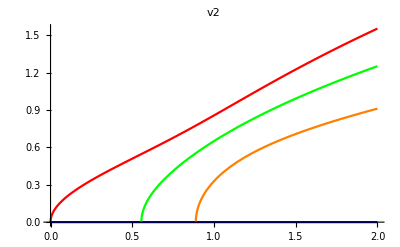

```mathematica
Plot[{0,(√(-g^3 (2+g) (5 (6+b)+(1+b) (8+3 b) g) (-5+(4+b) g+√(9+6 (-4+b) g+(4+b)^2 g^2))))/(2 √2 √(-g^3 (2+g) (5 (6+b)+(1+b) (8+3 b) g)))/.b->.8,((√(-g^3 (2+g) (5 (6+b)+(1+b) (8+3 b) g) (-6+(2+b) g+√(16+(2+b)^2 g^2)+√(-4 (-5+√(16+(2+b)^2 g^2))+2 g (-4+b (-2+(2+b) g+√(16+(2+b)^2 g^2)))))))/(2 √(-g^3 (2+g) (5 (6+b)+(1+b) (8+3 b) g))))/.b->.8,((√(-g^3 (2+g) (5 (6+b)+(1+b) (8+3 b) g) (-6+(2+b) g+√(16+(2+b)^2 g^2)-√(-4 (-5+√(16+(2+b)^2 g^2))+2 g (-4+b (-2+(2+b) g+√(16+(2+b)^2 g^2)))))))/(2 √(-g^3 (2+g) (5 (6+b)+(1+b) (8+3 b) g))))/.b->.8},{g,0,2},PlotLabel->"v2",PlotStyle->{Blue,Green,Red,Orange}]
```

```mathematica
FortranForm[{√(-1+g+b g),(√(-5+(4+b) g+√(9+6 (-4+b) g+(4+b)^2 g^2)))/(2 √2),1/2 √(-6+(2+b) g+√(16+(2+b)^2 g^2)-√(-4 (-5+√(16+(2+b)^2 g^2))+2 g (-4+b (-2+(2+b) g+√(16+(2+b)^2 g^2))))),1/2 √(-6+(2+b) g+√(16+(2+b)^2 g^2)+√(-4 (-5+√(16+(2+b)^2 g^2))+2 g (-4+b (-2+(2+b) g+√(16+(2+b)^2 g^2)))))}]
```

List(Sqrt(-1 + 1.8*g),Sqrt(-5 + (4 + b)*g + Sqrt(9 + 6*(-4 + b)*g + (4 + b)**2*g**2))/
     -   (2.*Sqrt(2)),Sqrt(-6 + (2 + b)*g + Sqrt(16 + (2 + b)**2*g**2) - 
     -     Sqrt(-4*(-5 + Sqrt(16 + (2 + b)**2*g**2)) + 
     -       2*g*(-4 + b*(-2 + (2 + b)*g + Sqrt(16 + (2 + b)**2*g**2)))))/2.,
     -  Sqrt(-6 + (2 + b)*g + Sqrt(16 + (2 + b)**2*g**2) + 
     -     Sqrt(-4*(-5 + Sqrt(16 + (2 + b)**2*g**2)) + 
     -       2*g*(-4 + b*(-2 + (2 + b)*g + Sqrt(16 + (2 + b)**2*g**2)))))/2.)

```mathematica
FortranForm[FullSimplify[{0,(√(-g^3 (2+g) (5 (6+b)+(1+b) (8+3 b) g) (-5+(4+b) g+√(9+6 (-4+b) g+(4+b)^2 g^2))))/(2 √2 √(-g^3 (2+g) (5 (6+b)+(1+b) (8+3 b) g))),((√(-g^3 (2+g) (5 (6+b)+(1+b) (8+3 b) g) (-6+(2+b) g+√(16+(2+b)^2 g^2)+√(-4 (-5+√(16+(2+b)^2 g^2))+2 g (-4+b (-2+(2+b) g+√(16+(2+b)^2 g^2)))))))/(2 √(-g^3 (2+g) (5 (6+b)+(1+b) (8+3 b) g)))),((√(-g^3 (2+g) (5 (6+b)+(1+b) (8+3 b) g) (-6+(2+b) g+√(16+(2+b)^2 g^2)-√(-4 (-5+√(16+(2+b)^2 g^2))+2 g (-4+b (-2+(2+b) g+√(16+(2+b)^2 g^2)))))))/(2 √(-g^3 (2+g) (5 (6+b)+(1+b) (8+3 b) g))))}]]
```

List(0,Sqrt(-(g**3*(2 + g)*(5*(6 + b) + (1 + b)*(8 + 3*b)*g)*(-5 + (4 + b)*g + Sqrt(9 + 6*(-4 + b)*g + (4 + b)**2*g**2))))/
     -   (2.*Sqrt(2)*Sqrt(-(g**3*(2 + g)*(5*(6 + b) + (1 + b)*(8 + 3*b)*g)))),
     -  Sqrt(-(g**3*(2 + g)*(5*(6 + b) + (1 + b)*(8 + 3*b)*g)*(-6 + (2 + b)*g + Sqrt(16 + (2 + b)**2*g**2) + 
     -         Sqrt(-4*(-5 + Sqrt(16 + (2 + b)**2*g**2)) + 2*g*(-4 + b*(-2 + (2 + b)*g + Sqrt(16 + (2 + b)**2*g**2)))))))/(2.*Sqrt(-(g**3*(2 + g)*(5*(6 + b) + (1 + b)*(8 + 3*b)*g)))),
     -  Sqrt(-(g**3*(2 + g)*(5*(6 + b) + (1 + b)*(8 + 3*b)*g)*(-6 + (2 + b)*g + Sqrt(16 + (2 + b)**2*g**2) - 
     -         Sqrt(-4*(-5 + Sqrt(16 + (2 + b)**2*g**2)) + 2*g*(-4 + b*(-2 + (2 + b)*g + Sqrt(16 + (2 + b)**2*g**2)))))))/(2.*Sqrt(-(g**3*(2 + g)*(5*(6 + b) + (1 + b)*(8 + 3*b)*g)))))

```mathematica
(√(-g^3 (2+g) (5 (6+b)+(1+b) (8+3 b) g) (-5+(4+b) g+√(9+6 (-4+b) g+(4+b)^2 g^2))))/(2 √2 √(-g^3 (2+g) (5 (6+b)+(1+b) (8+3 b) g)))/.b->.8/.g->.9
```

0.563712+0. ⅈ